## Double Pendulum

## Completed and Analyzed in class, February 25, 2025

This is the tenth notebook for you to complete.

### Double Pendulum — Angular Accelerations — Recap

Copied over from the theory we just examined, which used the simplifying values, m_2/m_1=1/3, L_2/L_1=1/4, and g/L_1=4 π^2, we have:

α_1=(-28 π^2 sinθ_1-4 π^2 sin(θ_1-2 θ_2)-2sin(θ_1-θ_2)(1/4 ω_2^2+ω_1^2 cos(θ_1-θ_2)))/(7-cos2(θ_1-θ_2)))

α_2=(8sin(θ_1-θ_2)(4 ω_1^2+16 π^2 cosθ_1+1/4 cos(θ_1-θ_2)))/(7-cos2(θ_1-θ_2))

```mathematica
alpha1[theta1_,theta2_,omega1_,omega2_]:=1/(7-Cos[2(theta1-theta2)])(-28 Pi^2 Sin[theta1]-4 Pi^2 Sin[theta1-2theta2]-2Sin[theta1-theta2](1/4 omega2^2+omega1^2 Cos[theta1-theta2]));

alpha2[theta1_,theta2_,omega1_,omega2_]:=1/(7-Cos[2(theta1-theta2)])8Sin[theta1-theta2](4 omega1^2+16 Pi^2 Cos[theta1]+1/4 Cos[theta1-theta2]);
```

### Initial Conditions

First set up the duration. Let’s also define steps and deltaT while we are at it:

```mathematica
tInitial = 0.0;
tFinal = 20.0;
steps = 60000;
deltaT = (tFinal - tInitial)/steps;
```

We’ll start the pendulum horizontally:

```mathematica
theta1Initial=-90°;
theta2Initial=90°;
omega1Initial=0.0;
omega2Initial=0.0;
```

```mathematica
initialConditions={tInitial,theta1Initial,theta2Initial,omega1Initial,omega2Initial};
```

“Goofer King” likes to start his horizontally in his YouTube video:

-Graphics-

### Second-Order Runge-Kutta — Double Pendulum — Recap

Also copied over from the theory:

t_(i+1)=t_i+Δt

θ_1^*=θ_1(t_i)+ω_1(t_i)·Δt/2

θ_2^*=θ_2(t_i)+ω_2(t_i)·Δt/2

ω_1^*=ω_1(t_i)+α_1(θ_1(t_i),θ_2(t_i),ω_1(t_i),ω_2(t_i))·Δt/2

ω_2^*=ω_2(t_i)+α_2(θ_1(t_i),θ_2(t_i),ω_1(t_i),ω_2(t_i))·Δt/2

ω_1(t_(i+1))=ω_1(t_i)+α_1(θ_1^*,θ_2^*,ω_1^*,ω_2^*)·Δt

ω_2(t_(i+1))=ω_2(t_i)+α_2(θ_1^*,θ_2^*,ω_1^*,ω_2^*)·Δt

θ_1(t_(i+1))=θ_1(t_i)+ (ω_1(t_i)+ω_1(t_(i+1)))Δt/2

θ_2(t_(i+1))=θ_2(t_i)+ (ω_2(t_i)+ω_2(t_(i+1)))Δt/2

### Second-Order Runge-Kutta — Implementation

```mathematica
rungeKutta2[cc_]:=(
curTime=cc[[1]];
curTheta1=cc[[2]];
curTheta2=cc[[3]];
curOmega1=cc[[4]];
curOmega2=cc[[5]];
newTime=curTime+deltaT;
theta1Star=curTheta1+curOmega1 deltaT/2;
theta2Star=curTheta2+curOmega2 deltaT/2;
omega1Star=curOmega1+alpha1[curTheta1,curTheta2,curOmega1,curOmega2] deltaT/2;
omega2Star=curOmega2+alpha2[curTheta1,curTheta2,curOmega1,curOmega2] deltaT/2;
newOmega1=curOmega1+alpha1[theta1Star,theta2Star,omega1Star,omega2Star]deltaT;
newOmega2=curOmega2+alpha2[theta1Star,theta2Star,omega1Star,omega2Star]deltaT;
newTheta1=curTheta1+(curOmega1+newOmega1)deltaT/2;
newTheta2=curTheta2+(curOmega2+newOmega2)deltaT/2;
{newTime,newTheta1,newTheta2,newOmega1,newOmega2}
)
rungeKutta2[initialConditions]
(* I get {0.000333333,-1.57079,1.5708,0.0131595,1.35978 x10^-20}. *)
```

{0.000333333,-1.57079,1.5708,0.0131595,1.35978×10^-20}

#### Using NestList[] to Repeatedly Apply rungeKutta2[]

```mathematica
rk2Results=Transpose[NestList[rungeKutta2,initialConditions,steps]];
```

#### Transposing to Get Points We Can Put in ListLinePlot[]

```mathematica
times=rk2Results[[1]];
theta1s=rk2Results[[2]];
theta2s=rk2Results[[3]];
```

```mathematica
timesAndTheta1s=Transpose[{times,theta1s}];
timesAndTheta2s=Transpose[{times,theta2s}];
```

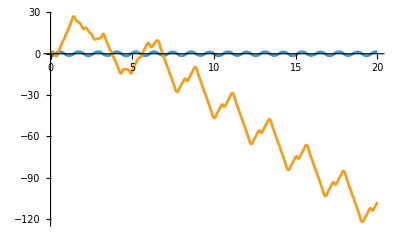

```mathematica
ListLinePlot[{timesAndTheta1s,timesAndTheta2s}]
```

#### A Graphic

The graphics work is straightforward but a little time-consuming, and not terribly instructive, so it is already all done:

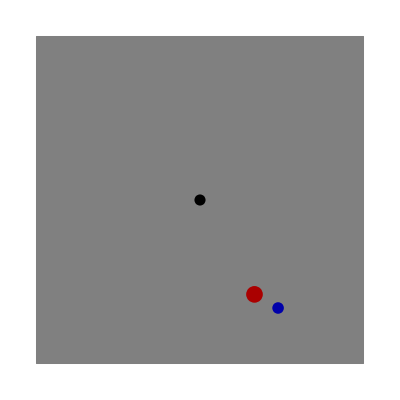

```mathematica
largerPointSize=0.03;
smallerPointSize=N[largerPointSize/Power[3,1/3]];
largerRodLength=4;
smallerRodLength=1;
doublePendulumGraphic[{theta1_,theta2_}]:=Graphics[{
buffer=1.0;
halfWidth=largerRodLength+smallerRodLength+buffer;
pivotPoint={0.0,0.0};
mass1Point=largerRodLength{Sin[theta1],-Cos[theta1]};
mass2Offset=smallerRodLength{Sin[theta2],-Cos[theta2]};
mass2Point=mass1Point+mass2Offset;
(* the next line makes a gray square *)
{EdgeForm[Thin],Gray,Polygon[{{-halfWidth,-halfWidth},{-halfWidth,halfWidth},{halfWidth,halfWidth},{halfWidth,-halfWidth}}]},
(* the next two lines make the rods that hold the masses *)
(* finally we draw the center and the masses *)
Style[Point[pivotPoint],PointSize[0.02]],
Style[Point[mass1Point],PointSize[largerPointSize],Darker[Red]],
Style[Point[mass2Point],PointSize[smallerPointSize],Darker[Blue]]
}]
(* A little test to see if our code at least draws equally-spaced points when the positions are all zero: *)
doublePendulumGraphic[{30°,60°}]
```

#### Animating The Graphics

```mathematica
theta1sAndtheta2s=Transpose[{theta1s,theta2s}];
slomoFactor=3;
Animate[doublePendulumGraphic[theta1sAndtheta2s[[i]]],{i,1,steps,1},DefaultDuration->slomoFactor(tFinal-tInitial)]
```

#### Comparing with YouTube

Check out Goofer King’s video of the crazy, chaotic double pendulum, https://youtu.be/6nhzrq4ALMc.

Here is an Oxford Mathematics professor admiring a similar setup: https://youtu.be/hv4fFWncyfM.